```mathematica
w={{-2.7337094640794124,-0.7702140555857921,0.0,1.6567767614014497,3.6202721698950695,5.58376757838869,7.54726298688231},{2.91935754756635,2.9193018984976185,2.919149531082956,2.9189406059691754,2.918730766273276,2.918576569668393,2.9185200059915593},{2.869666157397763,2.8695376381538646,2.8691853584599363,2.868701376142697,2.8682141788964395,2.8678554691364258,2.8677237347554585},{2.713959820164382,2.713415401434861,2.7119181274203017,2.709849095315628,2.7077521819907435,2.7061991384677597,2.7056268314494702},{0.0,0.0,0.0,0.0,0.0,0.0,0.0},{-2.7056268314494702,-2.7061991384677597,-2.7077521819907435,-2.709849095315628,-2.7119181274203017,-2.713415401434861,-2.7139598201643813},{-2.8677237347554585,-2.8678554691364258,-2.8682141788964395,-2.868701376142697,-2.8691853584599363,-2.8695376381538646,-2.869666157397763},{-2.9185200059915593,-2.918576569668393,-2.918730766273276,-2.9189406059691754,-2.919149531082956,-2.9193018984976185,-2.91935754756635},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815},{1.6939053807497815,1.3938428323076018,0.6768341894683341,0.0,-0.6768341894683334,-1.3938428323076013,-1.6939053807497815}};
```

```mathematica
w//MatrixForm
```

(-2.73371 | -0.770214 | 0. | 1.65678 | 3.62027 | 5.58377 | 7.54726
2.91936 | 2.9193 | 2.91915 | 2.91894 | 2.91873 | 2.91858 | 2.91852
2.86967 | 2.86954 | 2.86919 | 2.8687 | 2.86821 | 2.86786 | 2.86772
2.71396 | 2.71342 | 2.71192 | 2.70985 | 2.70775 | 2.7062 | 2.70563
0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.70563 | -2.7062 | -2.70775 | -2.70985 | -2.71192 | -2.71342 | -2.71396
-2.86772 | -2.86786 | -2.86821 | -2.8687 | -2.86919 | -2.86954 | -2.86967
-2.91852 | -2.91858 | -2.91873 | -2.91894 | -2.91915 | -2.9193 | -2.91936
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391
1.69391 | 1.39384 | 0.676834 | 0. | -0.676834 | -1.39384 | -1.69391)

```mathematica
w[[1]]
```

{-2.73371,-0.770214,0.,1.65678,3.62027,5.58377,7.54726}

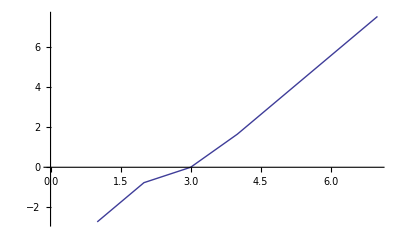

```mathematica
ListLinePlot[{w[[1]]}]
```

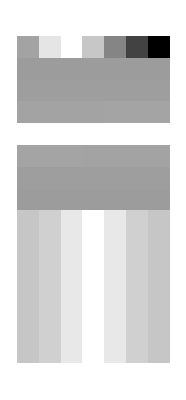

```mathematica
ArrayPlot[w]
```

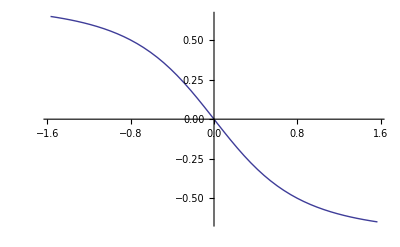

```mathematica
Plot[{Sin[(Sin[ArcTan[x1]]*Sin[-1])]},{x1,-Pi/2,Pi/2}]
```

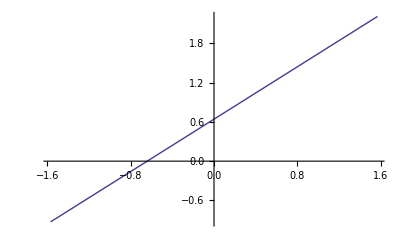

```mathematica
Plot[ArcTan[Exp[-Exp[-ArcTan[-1]^2]^2]]+x1,{x1,-Pi/2,Pi/2}]
```

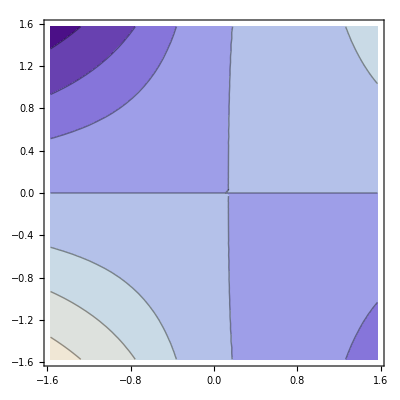

```mathematica
ContourPlot[x0*(((x1+ArcTan[-3.295894620950175])+Exp[-(x0*x1)^2])+x1),{x1,-Pi/2,Pi/2},{x0,-Pi/2,Pi/2}]
```